# Triangular Automata Package Demonstration

This is a Mathematica notebook that demonstrates how to use the functions of the Triangular Automata package to compute and display cellular automata in an infinite triangular grid.
Download the notebook: https://github.com/paulcousin/triangular-automata-mathematica 
More information: https://paulcousin.github.io/triangular-automata

Paul Cousin
https://orcid.org/0000-0002-3866-7615

## Introduction

Triangular Automata (TA) is a short name for cellular automata in a triangular grid. This package allows you to experiment with TA in a simple and efficient way.

## Setup

First, download the package from GitHub: https://github.com/paulcousin/triangular-automata-mathematica

To import it, place the TriangularAutomata.wl file in the same folder as your notebook and use the following command.

```mathematica
<<(NotebookDirectory[]<>"TriangularAutomata.wl");
```

## Rules

In this package, only a subset of possible TA called Elementary Triangular Automata (ETA) is considered. 

The restrictions are:

binary states:  s∈{0≡"dead"≡, 1≡"alive"≡}

only the first neighborhood is taken into account

orientation of the neighbors is not considered

This means that there are only 8 possible local configurations. They can be plotted with TAConfigurationPlot.

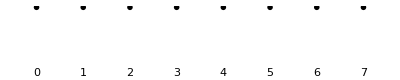

```mathematica
GraphicsGrid@{Table[TAConfigurationPlot[n],{n,0,7,1}],Range[0,7]}
```

A rule must the specify for every configuration, if the cell is going to be dead or alive at  t+1. There are thus only 2^8=256 rules. These rules can be indexed by a unique rule number n in the Wolfram Code style.

```mathematica
n=∑_(c=0)^7 2^c R[c]
```

Rules can be plotted with the TARulePlot function.

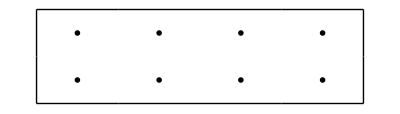
181  =  10110101_2
-Graphics-

```mathematica
TARulePlot[181, "Labeled"->True]
```

The “Labeled” option  adds the rule number in base 10 and in base 2 as a title. We can see that the behavior of the rule is capture in its binary digits. Starting from the right, they indicate the future state for each configuration as they have been ordered previously.

## Starting Points

Grids have a special format. They are captured in a list with three elements: a precursor of the adjacency matrix, a state vector and a coordinates vector. The first two are in the SparseArray format.

To simplify things, this package provides few starting points ready to use:

TAStartOneAlive: a grid with only one alive cell at the center

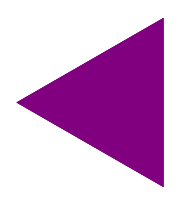

```mathematica
TAGridPlot@TAStartOneAlive
```

TAStartLogo: a grid with a logo that contains all 8 local configurations.

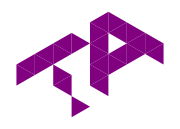

```mathematica
TAGridPlot@TAStartLogo
```

TAStartRandom[n]: a grid with cells randomly alive or dead on n layers.

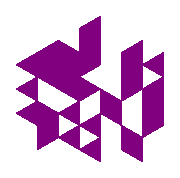

```mathematica
TAGridPlot@TAStartRandom[6]
```

## Evolution

We can now evolve these grids with different rules. The simplest function to do so is TAEvolve. Let’s use it to evolve TAStartOneAlive with rule 181.

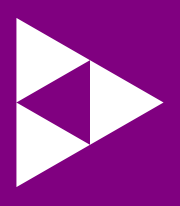

```mathematica
TAGridPlot@TAEvolve[TAStartOneAlive, 181]
```

As expected from the earlier plot of rule 181, the environment has become alive and we have three dead cells surrounding a central alive cell. It would be nice to see what will happen after that. The function TANestEvolve can be used to jump ahead several time steps. Let’s look at what TAStartOneAlive will look like after 64 time steps of evolution with rule 181.

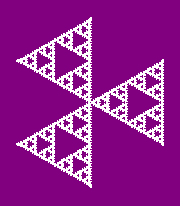

```mathematica
TAGridPlot@TANestEvolve[TAStartOneAlive, 181,64]
```

With this function, all the intermediate steps are lost and we only get the last grid. TANestListEvolve returns a list with all the intermediate steps.

```mathematica
GraphicsGrid@ArrayReshape[TAGridPlot[#]&/@TANestListEvolve[TAStartOneAlive, 181,64],{8,8}]
```

-Graphics-

TAEvolutionPlot shows an animated version of what we have just computed.

```mathematica
TAEvolutionPlot[TAStartOneAlive,181,64]
```

Like with Wolfram’s Elementary Automata, the grid evolution can be plotted all at once. But since each instant takes place in a 2D space, seeing the evolution in a single plot requires 3 dimensions. This plot  can be computed with TAEvolutionPlot3D. You can rotate it (in Mathematica) to see what it looks like from different angles.

```mathematica
TAEvolutionPlot3D[TAStartOneAlive,181,64]
```

-Graphics3D-

## Conclusion

I hope you will enjoy this package. Share what interesting things you find with it!